```mathematica
(* FUNCION PARA SOLUCIONAR LA ECUACION DIFERENCIAL DEL PENDULO EN UN RANGO DADO DE TIEMPO *)
SolvePend[ϕ0_,ω0_,L_,m_,η_,NNc_,T_,N_,plot_]:=Module[
(* PARAMETROS DE ENTRADA
 - ϕ0:   Posicion inicial,
  - ω0:   Velocidad inicial,
  - L:    Longitud del pendulo,
  - m:    Masa del pendulo,
  - η:    Viscosidad del medio,
  - NNc:  Torque externo relativo al torque critico,
  - T:    Tiempo total de simulacion,
  - N:    Numero de puntos de simulacion,
  - plot: (1) Retorna grafica de ϕ vs. t, (2) Retorna grafica de ω vs. t,
          (3) Retorna valor promedio de la velocidad angular, (Otro) Retorna "Error" *)

(* Definicion e inicializacion de variables locales *)
{g=9.8,ωc,Ω0,ϕant,ϕaant,ϕpres=ϕ0,dt,t,ϕlist={{0,ϕ0}},ωlist={{0,ω0}},plotϕ,plotω,ϕcalc=ϕ0,ωcalc=ω0,ωprom=ω0},
ωc=(m g L)/η;Ω0=√(g/L);dt=T/N;

(* Condicional que saca del programa si la opcion no es correcta *)
If[plot≠1&&plot≠2&&plot≠3,Print["Error"],
(* Posicion en ϕ(-dt) *)
ϕant=ϕ0-ω0 dt;
(* Ciclo que produce los datos *)
For[t=dt,t≤T,t=t+dt,
(* Guarda la posicion anterior antes de cambiarla *)
ϕaant=ϕcalc;
(* Calcula la posicion en el tiempo t usando la recursion de Verlet *)
ϕcalc=(2ϕcalc+(Ω0 dt)^2(NNc-Sin[ϕcalc])-(1-Ω0^2/(2 ωc)dt)ϕant)/(1+Ω0^2/(2 ωc)dt);
(* Calcula la velocidad en el tiempo t usando la definicion de derivada *)
ωcalc=(ϕcalc-ϕpres)/dt;
(* Guardamos la posicion dos tiempos antes y la posicion recien calculada *)
ϕant=ϕaant;ϕpres=ϕcalc;
(* Agrega los datos recien calculados a las listas de posicion y velocidad *)
AppendTo[ϕlist,{t,ϕcalc}];
AppendTo[ωlist,{t,ωcalc}]
];

(* Condicional para las opciones (1), (2), (3) *)
If[plot==1,
plotϕ=ListPlot[ϕlist,Frame->True,PlotRange->All,FrameLabel->{"Tiempo (s)","Posición Angular (rad)"},LabelStyle->Directive[Large],Joined->True,MeshStyle->Directive[PointSize[Small]]];
Return[plotϕ],
If[plot==2,
plotω=ListPlot[ωlist,Frame->True,PlotRange->All,FrameLabel->{"Tiempo (s)","Velocidad Angular (rad/s)"},LabelStyle->Directive[Large],Joined->True,MeshStyle->Directive[PointSize[Small]]];
Return[plotω],
If[plot==3,
For[i=1,i≤N,i++,
ωprom=ωprom+ωlist⟦i,2⟧
];ωprom=ωprom/(ωc N);
Return[ωprom]
]
]
]
]
];

(* FUNCION PARA GRAFICAR N/Nc CONTRA ⟨ω⟩/ωc *)
PlotNvsW[L_,m_,η_,Nmax_,dN_]:=Module[
(* PARAMETROS DE ENTRADA
 - L:    Longitud del pendulo,
  - m:    Masa del pendulo,
  - η:    Viscosidad del medio,
  - Nmax: Torque relativo maximo a graficar,
  - dN:   Paso del torque relativo *)

(* Definicion e inicializacion de variables locales *)
{ωplist={{0,0}},ωtlist={{0,0}},N,ωprom,ωteo,plot},

(* Ciclo para generar los puntos numericos y teoricos, usa la funcion SolvePend *)
For[N=dN,N≤Nmax,N=N+dN,
ωprom=SolvePend[0,0,L,m,η,N,10,20000,3];
AppendTo[ωplist,{ωprom,N}]
If[N≤1,ωteo=0;
AppendTo[ωtlist,{ωteo,N}],
ωteo=√(N^2-1);
AppendTo[ωtlist,{ωteo,N}]
]
];

(* Genera la grafica teorica y de la simulacion y la retorna *)
plot=ListPlot[{ωplist,ωtlist},Frame->True,PlotRange->All,FrameLabel->{("⟨ω⟩")/("ω_c"),("N")/("N_c")},LabelStyle->Directive[Large],Joined->True,PlotStyle->{{Thickness[.004]},{Hue[1,1,0.8],Thickness[.004],Dashed}}];
Return[plot]
];
```

```mathematica
Pη02N05=SolvePend[0,0,0.25,4,0.2,0.5,10,20000,1];
Pη02N10=SolvePend[0,0,0.25,4,0.2,1.0,10,20000,1];
Vη02N10=SolvePend[0,0,0.25,4,0.2,1.0,10,20000,2];
Pη10N05=SolvePend[0,0,0.25,4,10,0.5,10,20000,1];
Vη10N05=SolvePend[0,0,0.25,4,10,0.5,10,20000,2];
Pη10N20=SolvePend[0,0,0.25,4,10,2.0,10,20000,1];
Vη10N20=SolvePend[0,0,0.25,4,10,2.0,10,20000,2];
```

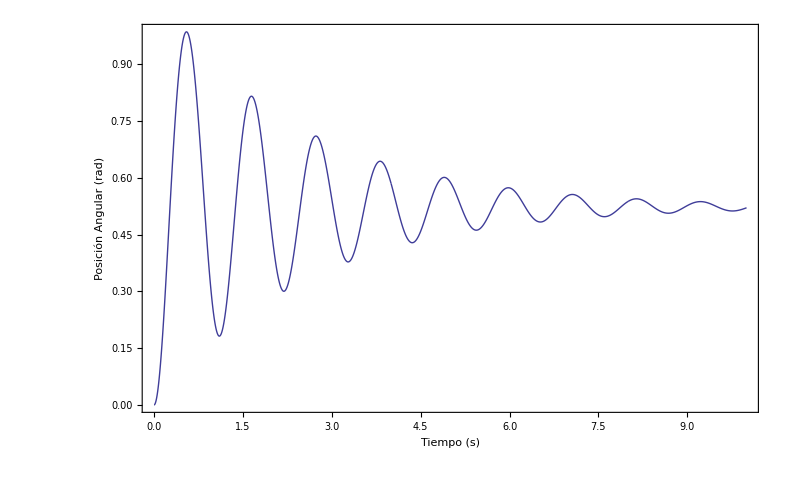

```mathematica
Show[Pη02N05]
```

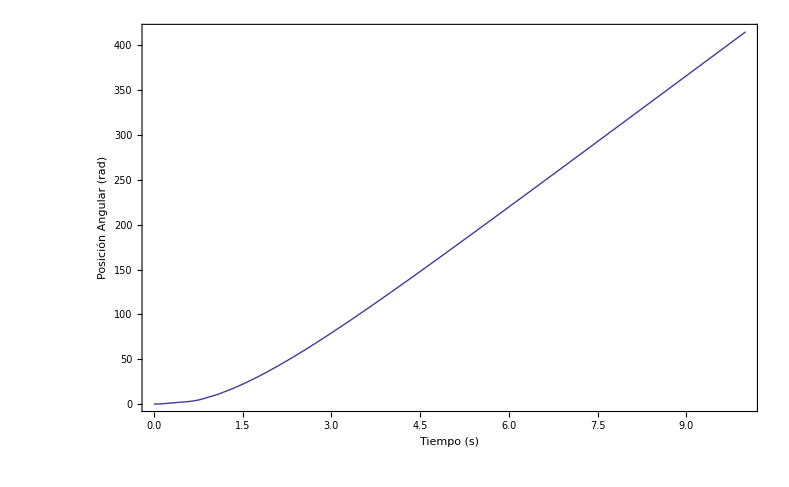

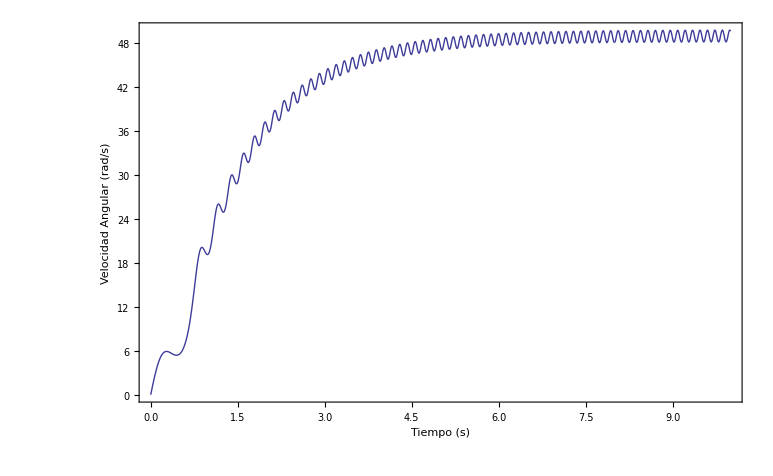

```mathematica
Show[Pη02N10]
Show[Vη02N10]
```

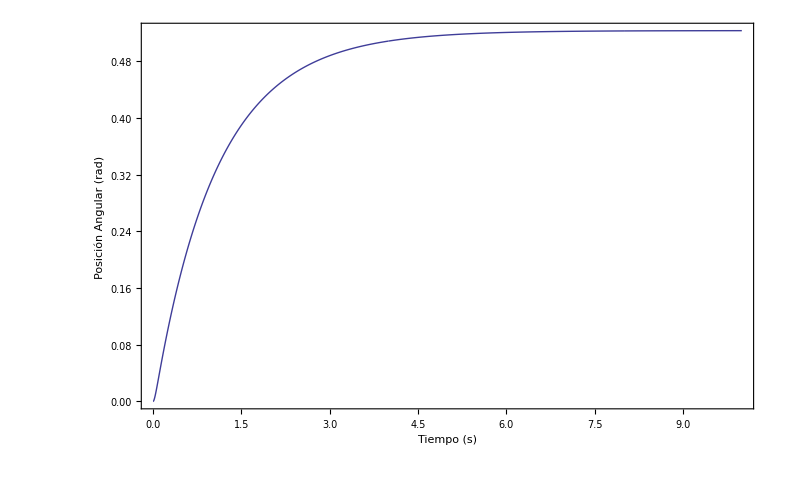

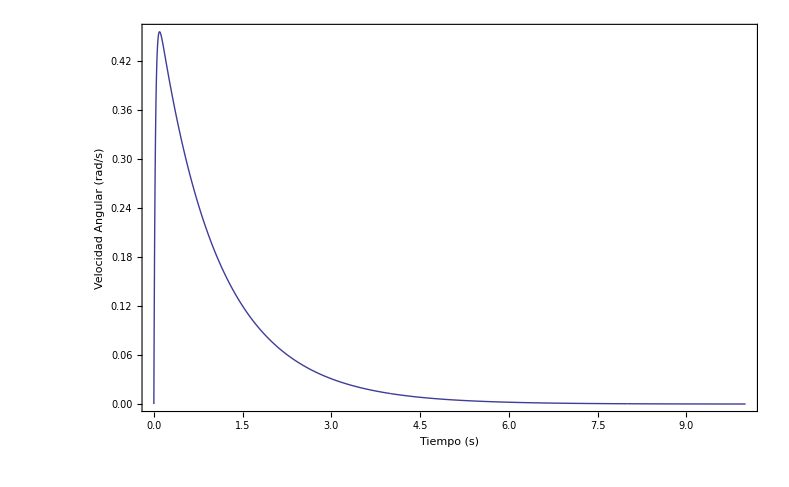

```mathematica
Show[Pη10N05]
Show[Vη10N05]
```

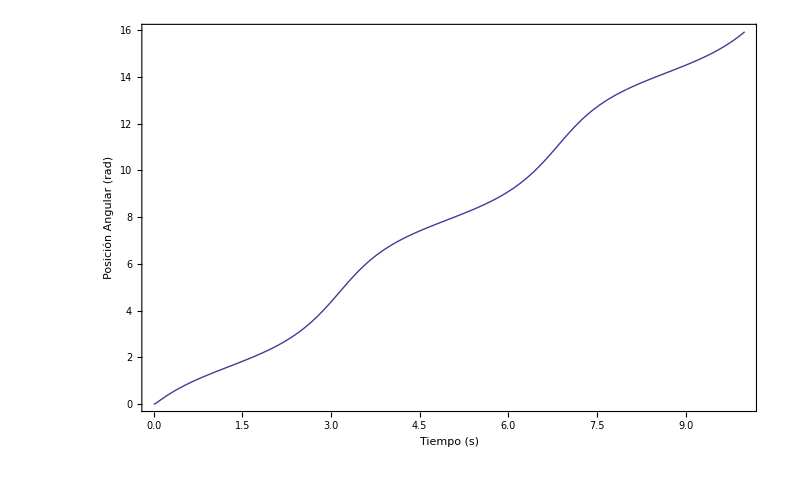

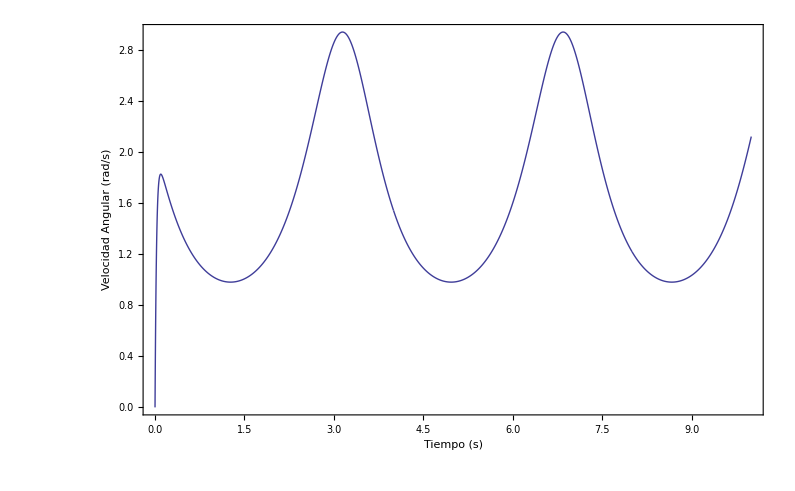

```mathematica
Show[Pη10N20]
Show[Vη10N20]
```

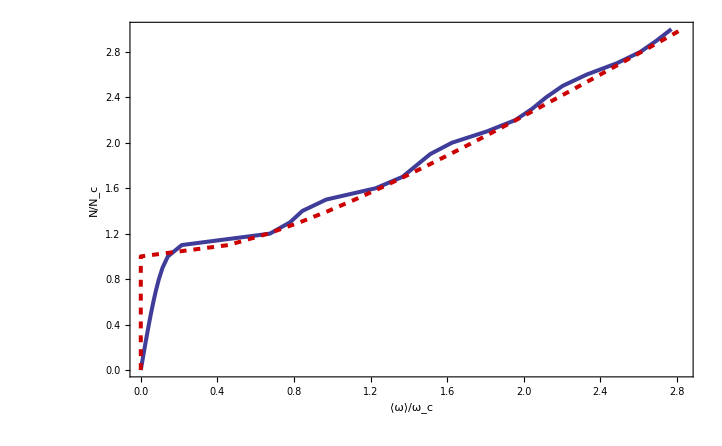

```mathematica
granplot=PlotNvsW[0.25,4,10,3,0.1]
```

```mathematica
Vη08N15=SolvePend[0,0,0.25,4,8,1.5,10,20000,2];
Vη08N50=SolvePend[0,0,0.25,4,8,5.0,10,20000,2];
```

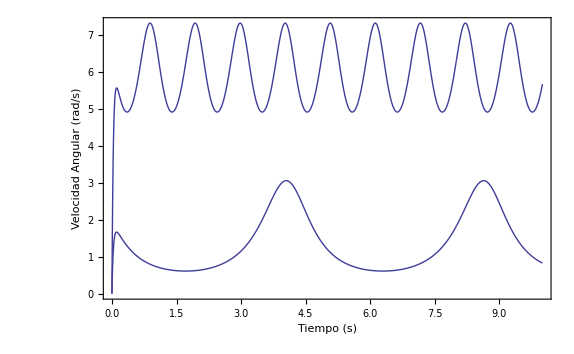

```mathematica
Show[Vη08N15,Vη08N50]
```